# Rigid bodies, plastic impact

```mathematica
param={l1->5.59,l2->5.59,m1->300,m2->300,mb->419725,mO->3000,r->0.12,γ->0.5};
paramExtraction={l1->5.59,l2->5.59,m1->300,m2->300,mb->419725,r->0.12,γ->0.5};
```

```mathematica
θ00=π/2;q10=0;q20=π/2;xb0=4;yb0=2;
```

```mathematica
paramScheme={θ0[t]->θ00,q1[t]->q10,q2[t]->q20,xb[t]->xb0,yb[t]->yb0};
```

## Kinematics

## Manipulator

We start with a simple manipulator, moving base (that mimics the spacecraft position and orientation) and two rotational links.

```mathematica
Mrotztrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
Mrotztrasl[α,{p1,p2,p3}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | p2
0 | 0 | 1 | p3
0 | 0 | 0 | 1)

```mathematica
Mfb=Mrotztrasl[0,{xb[t],yb[t],0}];
```

```mathematica
Mb0=Mrotztrasl[θ0[t],{0,0,0}];
```

```mathematica
Mf0=Mfb.Mb0;Mf0//MatrixForm
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | xb[t]
Sin[θ0[t]] | Cos[θ0[t]] | 0 | yb[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M01=Mrotztrasl[q1[t],{l1 Cos[q1[t]],l1 Sin[q1[t]],0}];M01//MatrixForm
```

(Cos[q1[t]] | -Sin[q1[t]] | 0 | l1 Cos[q1[t]]
Sin[q1[t]] | Cos[q1[t]] | 0 | l1 Sin[q1[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M12=Mrotztrasl[q2[t],{l2 Cos[q2[t]],l2 Sin[q2[t]],0}];M12//MatrixForm
```

(Cos[q2[t]] | -Sin[q2[t]] | 0 | l2 Cos[q2[t]]
Sin[q2[t]] | Cos[q2[t]] | 0 | l2 Sin[q2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M02=Simplify[M01.M12];
```

```mathematica
Mf1=Simplify[Mf0.M01];
```

```mathematica
Mf2=Simplify[Mf1.M12];
```

### Origin points

```mathematica
origin={0,0,0,1};
```

```mathematica
Ob=Mfb.origin;Ob//MatrixForm
```

(xb[t]
yb[t]
0
1)

```mathematica
O1=Mf1.origin;O1//MatrixForm
```

(l1 Cos[q1[t]+θ0[t]]+xb[t]
l1 Sin[q1[t]+θ0[t]]+yb[t]
0
1)

```mathematica
EE=Simplify[Mf2.origin];EE//MatrixForm
```

(l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]]+xb[t]
l1 Sin[q1[t]+θ0[t]]+l2 Sin[q1[t]+q2[t]+θ0[t]]+yb[t]
0
1)

Jacobian matrixOb:

```mathematica
J=FullSimplify[D[EE[[1;;2]],{{xb[t],yb[t],θ0[t],q1[t],q2[t]}}]];J//MatrixForm
```

(1 | 0 | -l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]] | -l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]] | -l2 Sin[q1[t]+q2[t]+θ0[t]]
0 | 1 | l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]] | l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]] | l2 Cos[q1[t]+q2[t]+θ0[t]])

```mathematica
J. D[{xb[t],yb[t],θ0[t],q1[t],q2[t]},t]==D[EE[[1;;2]],t]//Simplify
```

True

### Plot a 2D scheme of the robot

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.paramScheme,O1[[1;;2]]/.param/.paramScheme,EE[[1;;2]]/.param/.paramScheme},PlotMarkers->{Automatic, 5}];
```

```mathematica
labels={"xf","yf"};
```

```mathematica
For[i=1,i<3,i++,u={0,0};(*initializing u as a null 3 elements vector*)u⟦i⟧=1;(*Setting the i-th element of u equal to 1,to have a unit vector*)RF0arrow[i]=Graphics[{Thickness[0.010],Red,Arrowheads[0.04],
Text[labels⟦i⟧,2 u+0.07],Arrow[{{0,0},2 u}]},Axes->True]];
```

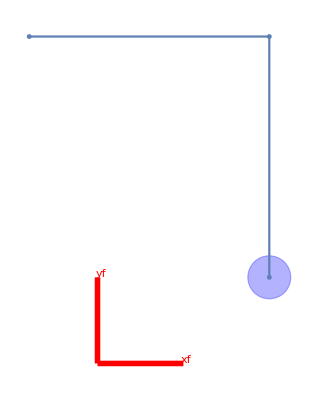

```mathematica
Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],RobotPlot,RF0arrow[1],RF0arrow[2]}]
```

```mathematica
paraml={l1->2.0,l2->3.0};
```

```mathematica
Manipulate[Show[{ListLinePlot[{Ob[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},O1[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},EE[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5}}/.paraml,PlotRange->{{-5,8},{-5,8}},AspectRatio->1,PlotMarkers->{Automatic, 5}]},Block[{r=0.5},Graphics[{EdgeForm[Thick],Blue,Opacity[0.3],Disk[Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},r],Thickness[0.007],Opacity[0.5],Red,Arrowheads[0.04],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]+l1 /.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]/.paraml/.paramScheme}}],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1/.paraml/.paramScheme}}],Blue,Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]-l1 Sin[a3]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1 Cos[a3]/.paraml/.paramScheme}}],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]+l1 Cos[a3]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1 Sin[a3]/.paraml/.paramScheme}}]}]],RF0arrow[1],RF0arrow[2]],{a1,0,3},{a2,0,3},{a3,0,π/4},{a4,0,π/4},{a5,0,π/4}]
```

## Object

-Graphics-

Let’s consider a circula spinning satellite. In 2D, we have 3 DoF: xb, yOb, and rotation around z.
Coordinats refered to the COM:

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

The jacobian describe the relationship between the velocityOb of the dof and the contact point:

```mathematica
MfO0=Mrotztrasl[0,{xO[t],yO[t],0}];MfO0//MatrixForm
```

(1 | 0 | 0 | xO[t]
0 | 1 | 0 | yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO0O1=Mrotztrasl[Ω[t],{0,0,0}];MO0O1//MatrixForm
```

(Cos[Ω[t]] | -Sin[Ω[t]] | 0 | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO1O2=Mrotztrasl[γ,{r Cos[γ] ,r Sin[γ],0}];MO1O2//MatrixForm
```

(Cos[γ] | -Sin[γ] | 0 | r Cos[γ]
Sin[γ] | Cos[γ] | 0 | r Sin[γ]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MfO1=MfO0.MO0O1;
MfO2=Simplify[MfO0.MO0O1.MO1O2];MfO2//MatrixForm
```

(Cos[γ+Ω[t]] | -Sin[γ+Ω[t]] | 0 | r Cos[γ+Ω[t]]+xO[t]
Sin[γ+Ω[t]] | Cos[γ+Ω[t]] | 0 | r Sin[γ+Ω[t]]+yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
contactP=(MfO2.{0,0,0,1})[[1;;2]];contactP//MatrixForm
velContactP=D[contactP,t];velContactP//MatrixForm
```

(r Cos[γ+Ω[t]]+xO[t]
r Sin[γ+Ω[t]]+yO[t])

(xO'[t]-r Sin[γ+Ω[t]] Ω'[t]
yO'[t]+r Cos[γ+Ω[t]] Ω'[t])

```mathematica
Jo=D[contactP,{{xO[t],yO[t],Ω[t]}}];Jo//MatrixForm
```

(1 | 0 | -r Sin[γ+Ω[t]]
0 | 1 | r Cos[γ+Ω[t]])

```mathematica
Transpose[Jo]//MatrixForm
```

(1 | 0
0 | 1
-r Sin[γ+Ω[t]] | r Cos[γ+Ω[t]])

```mathematica
Jo.ψ'==velContactP//Simplify
```

True

## Dynamics

## Manipulator

### IR method

The mass is considered distributed, hence the pseudo inertia tensor can be written like this:

```mathematica
Ixb=1/4 mb r^2;
Iyb=1/4 mb r^2;
Izb=0;
Ix1=1/3m1 l1^2;
Ix2=1/3 m2 l2^2;
```

Inertia frame in the com of the round base:

```mathematica
J00={{Ixb,0,0,0},{0,Iyb,0,0},{0,0,Izb,0},{0,0,0,mb}};J00//MatrixForm
```

((mb r^2)/4 | 0 | 0 | 0
0 | (mb r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mb)

```mathematica
J0f=Simplify[Mf0.J00.Transpose[Mf0]];J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
J11={{Ix1,0,0,-l1/2 m1},{0,0,0,0},{0,0,0,0},{-l1/2 m1,0,0,m1}};J11//MatrixForm
```

((l1^2 m1)/3 | 0 | 0 | -(l1 m1)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l1 m1)/2 | 0 | 0 | m1)

```mathematica
J1f=Simplify[Mf1.J11.Transpose[Mf1]];
```

```mathematica
J22={{Ix2,0,0,-l2/2 m2},{0,0,0,0},{0,0,0,0},{-l2/2 m2,0,0,m2}};J22//MatrixForm
```

((l2^2 m2)/3 | 0 | 0 | -(l2 m2)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l2 m2)/2 | 0 | 0 | m2)

```mathematica
J2f=Simplify[Mf2.J22.Transpose[Mf2]];
```

```mathematica
Wf0=Simplify[D[Mf0,t].Inverse[Mf0]];Wf0//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb=Simplify[D[Mfb,t].Inverse[Mfb]];Wfb//MatrixForm
```

(0 | 0 | 0 | xb'[t]
0 | 0 | 0 | yb'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0=Simplify[D[Mb0,t].Inverse[Mb0]];Wb0//MatrixForm
```

(0 | -θ0'[t] | 0 | 0
θ0'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0Ff=Simplify[Mfb.Wb0.Inverse[Mfb]];Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | yb[t] θ0'[t]
θ0'[t] | 0 | 0 | -xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb+Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Lfbx=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Lfby=({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Lb0=Wb0/θ0'[t];
```

```mathematica
Lb0Ff=Simplify[Mf0.Lb0.Inverse[Mf0]];Lb0Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];W01//MatrixForm
```

(0 | -q1'[t] | 0 | 0
q1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L01=W01/q1'[t];
```

```mathematica
L01Ff=Simplify[Mf0.L01.Inverse[Mf0]];L01Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf1=Simplify[D[Mf1,t].Inverse[Mf1]];Wf1//MatrixForm
```

(0 | -q1'[t]-θ0'[t] | 0 | xb'[t]+yb[t] (q1'[t]+θ0'[t])
q1'[t]+θ0'[t] | 0 | 0 | yb'[t]-xb[t] (q1'[t]+θ0'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W12=Simplify[D[M12,t].Inverse[M12]];W12//MatrixForm
```

(0 | -q2'[t] | 0 | 0
q2'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L12=W12/q2'[t];
L12Ff=Simplify[Mf1.L12.Inverse[Mf1]];L12Ff//MatrixForm
```

(0 | -1 | 0 | l1 Sin[q1[t]+θ0[t]]+yb[t]
1 | 0 | 0 | -l1 Cos[q1[t]+θ0[t]]-xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf2=Simplify[D[Mf2,t].Inverse[Mf2]];Wf2//MatrixForm
```

(0 | -q1'[t]-q2'[t]-θ0'[t] | 0 | l1 Sin[q1[t]+θ0[t]] q2'[t]+xb'[t]+yb[t] (q1'[t]+q2'[t]+θ0'[t])
q1'[t]+q2'[t]+θ0'[t] | 0 | 0 | -l1 Cos[q1[t]+θ0[t]] q2'[t]+yb'[t]-xb[t] (q1'[t]+q2'[t]+θ0'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
T1=Simplify[1/2Tr[Wf0.J0f.Transpose[Wf0]]];
T2=Simplify[1/2Tr[Wf1.J1f.Transpose[Wf1]]];
T3=Simplify[1/2Tr[Wf2.J2f.Transpose[Wf2]]];
```

The potential energy of body i, denoted by Ui, consists of two parts; one due to the gravity gradient and the other due to the elastic strain energy stored in the flexbible body. The effect of the former is much smaller than the latter and is neglected here. Hence the potential energy of a rigid body is equal to zero.

```mathematica
L=T1+T2+T3;
```

ByOb neglecting the constraints forces (since theyOb don’t affect the lagrange equation), we get the actions matrices:

```mathematica
actionMatrix[cx_,cy_,cz_,fx_,fy_,fz_]:={{0,-cz,cy,fx},{cz,0,-cx,fy},{-cy,cx,0,fz},{-fx,-fy,-fz,0}};
```

```mathematica
ϕ0b=actionMatrix[0,0,τ1-τ2,Fx,Fy,0];ϕ0b//MatrixForm
```

(0 | -τ1+τ2 | 0 | Fx
τ1-τ2 | 0 | 0 | Fy
0 | 0 | 0 | 0
-Fx | -Fy | 0 | 0)

```mathematica
ϕbf=FullSimplify[Mf0.ϕ0b.Transpose[Mf0]];
```

```mathematica
ϕ11=actionMatrix[0,0,τ2-τ3,0,0,0];ϕ11//MatrixForm
ϕ1f=FullSimplify[Mf1.ϕ11.Transpose[Mf1]];ϕ1f//MatrixForm
```

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ϕ22=actionMatrix[0,0,τ3,0,0,0];
ϕ2f=FullSimplify[Mf2.ϕ22.Transpose[Mf2]];
```

Let’s derivate the non-lagrangian components:

```mathematica
PSS[Mat1_,Mat2_]:=Mat1[[3,2]]*Mat2[[3,2]]+Mat1[[1,3]]*Mat2[[1,3]]+Mat1[[2,1]]*Mat2[[2,1]]+Mat1[[1,4]]*Mat2[[1,4]]+Mat1[[2,4]]*Mat2[[2,4]]+Mat1[[3,4]]*Mat2[[3,4]];
```

```mathematica
f1=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfbx]]
f2=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfby]]
f3=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lb0Ff]]
f4=FullSimplify[PSS[(ϕ1f+ϕ2f),L01Ff]]
f5=Simplify[PSS[(ϕ2f),L12Ff]]
```

Fx Cos[θ0[t]]-Fy Sin[θ0[t]]

Fy Cos[θ0[t]]+Fx Sin[θ0[t]]

τ1

τ2

τ3

```mathematica
eq1=Simplify[D[D[L,xb'[t]],t]-D[L,xb[t]]-f1];
eq2=Simplify[D[D[L,yb'[t]],t]-D[L,yb[t]]-f2];
eq3=Simplify[D[D[L,θ0'[t]],t]-D[L,θ0[t]]-f3];
eq4=Simplify[D[D[L,q1'[t]],t]-D[L,q1[t]]-f4];
eq5=Simplify[D[D[L,q2'[t]],t]-D[L,q2[t]]-f5];
```

```mathematica
{c,A}=FullSimplify[Normal@CoefficientArrays[{eq1,eq2,eq3,eq4,eq5},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Fx,Fy,τ1,τ2,τ3}]];
M=A[[1;;5,1;;5]];
u=-A[[1;;5,6;;10]];
```

```mathematica
MatrixForm[M]
```

(m1+m2+mb | 0 | 1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | -1/2 l2 m2 Sin[q1[t]+q2[t]+θ0[t]]
0 | m1+m2+mb | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/2 l2 m2 Cos[q1[t]+q2[t]+θ0[t]]
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/6 (2 l2^2 m2+2 l1^2 (m1+3 m2)+3 mb r^2+6 l1 l2 m2 Cos[q2[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]])
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]])
-1/2 l2 m2 Sin[q1[t]+q2[t]+θ0[t]] | 1/2 l2 m2 Cos[q1[t]+q2[t]+θ0[t]] | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]]) | (l2^2 m2)/3)

```mathematica
MatrixForm[u]
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | 0 | 0
Sin[θ0[t]] | Cos[θ0[t]] | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[c]
```

(1/2 (-l1 (m1+2 m2) Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-l2 m2 Cos[q2[t]] Cos[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2+l2 m2 Sin[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-l2 m2 Cos[q1[t]+θ0[t]] Sin[q2[t]] (q1'[t]+q2'[t]+θ0'[t])^2-l2 m2 Cos[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)
-1/2 l1 l2 m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])
-1/2 l1 l2 m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])
1/2 l1 l2 m2 Sin[q2[t]] (q1'[t]+θ0'[t])^2)

Equation of motion: Mp^(..)+ c = u

### Classic Lagrangian method

```mathematica
Ob2D=(Mfb.{0,0,0,1})[[1;;2]];
O12D=(Mf1.{-l1/2,0,0,1})[[1;;2]]
EE2D=(Mf2.{-l2/2,0,0,1})[[1;;2]];
```

{1/2 l1 Cos[q1[t]+θ0[t]]+xb[t],1/2 l1 Sin[q1[t]+θ0[t]]+yb[t]}

```mathematica
vb=D[Ob2D,t]
v1=D[O12D,t]
v2=D[EE2D,t]
```

{xb'[t],yb'[t]}

{xb'[t]-1/2 l1 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t]),yb'[t]+1/2 l1 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])}

{xb'[t]-l1 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-1/2 l2 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]),yb'[t]+l1 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])+1/2 l2 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])}

```mathematica
vbsquare=Simplify[vb[[1]]^2+vb[[2]]^2];
v1square=Simplify[v1[[1]]^2+v1[[2]]^2];
v2square=Simplify[v2[[1]]^2+v2[[2]]^2];
```

Inertia wrt CoM:

```mathematica
Ib=1/2mb r^2;
I1=1/12m1 l1^2;
I2=1/12m2 l2^2;
```

```mathematica
tb=1/2mb vbsquare+1/2Ib θ0'[t]^2;
t1=1/2m1 v1square+1/2I1 (θ0'[t]+q1'[t])^2;
t2=1/2m2 v2square+1/2I2 (θ0'[t]+q1'[t]+q2'[t])^2;
```

```mathematica
lmid=tb+t1+t2;
```

```mathematica
eq1Mid=Simplify[D[D[lmid,xb'[t]],t]-D[lmid,xb[t]]-f1];
eq2Mid=Simplify[D[D[lmid,yb'[t]],t]-D[lmid,yb[t]]-f2];
eq3Mid=Simplify[D[D[lmid,θ0'[t]],t]-D[lmid,θ0[t]]-f3];
eq4Mid=Simplify[D[D[lmid,q1'[t]],t]-D[lmid,q1[t]]-f4];
eq5Mid=Simplify[D[D[lmid,q2'[t]],t]-D[lmid,q2[t]]-f5];
```

```mathematica
{c2,A2}=FullSimplify[Normal@CoefficientArrays[{eq1Mid,eq2Mid,eq3Mid,eq4Mid,eq5Mid},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Fx,Fy,τ1,τ2,τ3}]];
M2=A2[[1;;5,1;;5]];
u2=-A2[[1;;5,6;;10]];
```

```mathematica
FullSimplify[c2-c]
```

{0,0,0,0,0}

```mathematica
FullSimplify[M[[1]]==M2[[1]]]
FullSimplify[M[[2]]==M2[[2]]]
FullSimplify[M[[3]]==M2[[3]]]
FullSimplify[M[[4]]==M2[[4]]]
FullSimplify[M[[5]]==M2[[5]]]
```

True

True

True

«2 more identical outputs»

## Object

### IR method

```mathematica
IxO=1/4 mO r^2;
IyO=1/4 mO r^2;
IzO=0;
```

```mathematica
JO1O1={{IxO,0,0,0},{0,IyO,0,0},{0,0,IzO,0},{0,0,0,mO}};JO1O1//MatrixForm
```

((mO r^2)/4 | 0 | 0 | 0
0 | (mO r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mO)

```mathematica
J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
JOf=Simplify[MfO1.JO1O1.Transpose[MfO1]];JOf//MatrixForm
```

(1/4 mO (r^2+4 xO[t]^2) | mO xO[t] yO[t] | 0 | mO xO[t]
mO xO[t] yO[t] | 1/4 mO (r^2+4 yO[t]^2) | 0 | mO yO[t]
0 | 0 | 0 | 0
mO xO[t] | mO yO[t] | 0 | mO)

```mathematica
WfO1=Simplify[D[MfO1,t].Inverse[MfO1]];WfO1//MatrixForm
```

(0 | -Ω'[t] | 0 | xO'[t]+yO[t] Ω'[t]
Ω'[t] | 0 | 0 | yO'[t]-xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1=Simplify[D[MO0O1,t].Inverse[MO0O1]];WO0O1//MatrixForm
```

(0 | -Ω'[t] | 0 | 0
Ω'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1Ff=FullSimplify[MfO0.WO0O1.Inverse[MfO0]];WO0O1Ff//MatrixForm
```

(0 | -Ω'[t] | 0 | yO[t] Ω'[t]
Ω'[t] | 0 | 0 | -xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LO0O1Ff=Simplify[WO0O1Ff/Ω'[t]];LO0O1Ff//MatrixForm
```

(0 | -1 | 0 | yO[t]
1 | 0 | 0 | -xO[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LfOx=Lfbx;
LfOy=Lfby;
```

```mathematica
ϕO1O1=actionMatrix[0,0,τO,FOx,FOy,0];
ϕO1O1Ff=FullSimplify[MfO1.ϕO1O1.Transpose[MfO1]];
```

```mathematica
f1O=FullSimplify[PSS[ϕO1O1Ff,LfOx]]
f2O=FullSimplify[PSS[ϕO1O1Ff,LfOy]]
f3O=FullSimplify[PSS[ϕO1O1Ff,LO0O1Ff]]
```

FOx Cos[Ω[t]]-FOy Sin[Ω[t]]

FOy Cos[Ω[t]]+FOx Sin[Ω[t]]

τO

```mathematica
TO=Simplify[1/2Tr[WfO1.JOf.Transpose[WfO1]]];
LO=TO;
```

```mathematica
eq1OIR=Simplify[D[D[LO,xO'[t]],t]-D[L,xO[t]]-f1O];
eq2OIR=Simplify[D[D[LO,yO'[t]],t]-D[L,yO[t]]-f2O];
eq3OIR=Simplify[D[D[LO,Ω'[t]],t]-D[L,Ω[t]]-f3O];
```

```mathematica
{co,Ao}=FullSimplify[Normal@CoefficientArrays[{eq1OIR,eq2OIR,eq3OIR},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}]];
Mo=Ao[[1;;3,1;;3]];
uo=-Ao[[1;;3,4;;6]];
```

```mathematica
Mo//MatrixForm
co//MatrixForm
uo//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

### Classic method

```mathematica
Iz=1/2mO r^2;
```

```mathematica
T=1/2 mO(ψ'[[1]]^2+ψ'[[2]]^2)+1/2Iz ψ'[[3]]^2;
```

```mathematica
eq1O=Simplify[D[D[T,xO'[t]],t]-D[T,xO[t]]-f1O];
eq2O=Simplify[D[D[T,yO'[t]],t]-D[T,yO[t]]-f2O];
eq3O=Simplify[D[D[T,Ω'[t]],t]-D[T,Ω[t]]-f3O];
```

```mathematica
{co2,Ao2}=Normal@CoefficientArrays[{eq1O,eq2O,eq3O},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}];
Mo2=Ao2[[1;;3,1;;3]];
uo2=-Ao2[[1;;3,4;;6]];
```

```mathematica
Mo2//MatrixForm
co2//MatrixForm
uo2//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

## Impact

## Pre-impact

Following the 2007 paper, we can find the final condition of the manipulator after the impact:

-Graphics-

```mathematica
Jo//MatrixForm
```

(1 | 0 | -r Sin[γ+Ω[t]]
0 | 1 | r Cos[γ+Ω[t]])

In the 2007 paper, there is an error when calculating the pseudo-inverse. The correct is the following:

```mathematica
pseudoInverseJo=Transpose[Jo].Inverse[Jo.Transpose[Jo]]//Simplify;pseudoInverseJo//MatrixForm
```

((2+r^2+r^2 Cos[2 (γ+Ω[t])])/(2 (1+r^2)) | (r^2 Cos[γ+Ω[t]] Sin[γ+Ω[t]])/(1+r^2)
(r^2 Cos[γ+Ω[t]] Sin[γ+Ω[t]])/(1+r^2) | (2+r^2-r^2 Cos[2 (γ+Ω[t])])/(2 (1+r^2))
-(r Sin[γ+Ω[t]])/(1+r^2) | (r Cos[γ+Ω[t]])/(1+r^2))

```mathematica
G=M+Transpose[J].Transpose[pseudoInverseJo].Mo.pseudoInverseJo.J//FullSimplify ;
```

```mathematica
Chop@Inverse[G/.Ω[t]->contactConditionP/.param/.paramScheme]//MatrixForm
```

```mathematica
p={xb[t],yb[t],θ0[t],q1[t],q2[t]};
p'=D[p,t];
```

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

```mathematica
H=M. p'+Transpose[J].Transpose[pseudoInverseJo].Mo.ψ'//Simplify;
```

Final values of the general coordinated of the base+manipulator after the impact:

```mathematica
Chop[H/.param/.paramScheme/.initialConditions1]//MatrixForm
```

{1/2 (-5031. q1'[t]+840650 xb'[t]+2957.41 (2.0144+0.0144 Cos[2 (0.5+Ω[t])]) xO'[t]+42.5868 Sin[2 (0.5+Ω[t])] yO'[t]-5031. θ0'[t]-5.11041 Sin[0.5+Ω[t]] Ω'[t]),1/2 (-1677. q1'[t]-1677. q2'[t]+42.5868 Sin[2 (0.5+Ω[t])] xO'[t]+840650 yb'[t]+2957.41 (2.0144-0.0144 Cos[2 (0.5+Ω[t])]) yO'[t]-1677. θ0'[t]+5.11041 Cos[0.5+Ω[t]] Ω'[t]),1/6 (93744.3 q1'[t]+18748.9 q2'[t]-15093. xb'[t]-8872.24 (5.59 (2.0144+0.0144 Cos[2 (0.5+Ω[t])])+0.080496 Sin[2 (0.5+Ω[t])]) xO'[t]-5031. yb'[t]+8872.24 (-5.59 (2.0144-0.0144 Cos[2 (0.5+Ω[t])])-0.080496 Sin[2 (0.5+Ω[t])]) yO'[t]+111876. θ0'[t]+15.3312 (5.59 Cos[1.0708-Ω[t]]+5.59 Cos[2.64159-Ω[t]]) Ω'[t]),1/6 (93744.3 q1'[t]+18748.9 q2'[t]-15093. xb'[t]-8872.24 (5.59 (2.0144+0.0144 Cos[2 (0.5+Ω[t])])+0.080496 Sin[2 (0.5+Ω[t])]) xO'[t]-5031. yb'[t]+8872.24 (-5.59 (2.0144-0.0144 Cos[2 (0.5+Ω[t])])-0.080496 Sin[2 (0.5+Ω[t])]) yO'[t]+93744.3 θ0'[t]+15.3312 (5.59 Cos[1.0708-Ω[t]]+5.59 Cos[2.64159-Ω[t]]) Ω'[t]),0.931667 (3354. q1'[t]+3354. q2'[t]-127.76 Sin[2.14159-2 Ω[t]] xO'[t]-900 yb'[t]+8872.24 (-2.0144-0.0144 Cos[2.14159-2 Ω[t]]) yO'[t]+3354. θ0'[t]+15.3312 Cos[2.64159-Ω[t]] Ω'[t])}/.initialConditions1

```mathematica
Transpose[J[[1;;2]]/.param/.paramScheme]//MatrixForm
Chop[Transpose[pseudoInverseJo].Mo.ψ'/.param/.paramScheme/.initialConditions1]//MatrixForm
```

(1 | 0
0 | 1
-5.59 | -5.59
-5.59 | -5.59
0. | -5.59)

{1478.71 (2.0144+0.0144 Cos[2 (0.5+Ω[t])]) xO'[t]+42.5868 Cos[0.5+Ω[t]] Sin[0.5+Ω[t]] yO'[t]-2.55521 Sin[0.5+Ω[t]] Ω'[t],42.5868 Cos[0.5+Ω[t]] Sin[0.5+Ω[t]] xO'[t]+1478.71 (2.0144-0.0144 Cos[2 (0.5+Ω[t])]) yO'[t]+2.55521 Cos[0.5+Ω[t]] Ω'[t]}/.initialConditions1

```mathematica
pf'=Inverse[G].H ;
```

Final values of the satellite after the impact:

```mathematica
ψf'=pseudoInverseJo.J.pf';
```

### Initial conditions

After the capture, we assume that the object is now perfectlyOb attached to the EE, hence the contact point’s variables coincides with the ones of the EE. We also assume that the spinning velocityOb is resetted:

```mathematica
EEi=EE[[1;;2]]/.param/.paramScheme
```

{-1.59,7.59}

Condition for alignment of the object with the EE:

```mathematica
contactCondition=(θ00+q10+q20+π-(γ/.param))
```

5.78319

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.12+xO[t],-2.93915×10^-17+yO[t]}

```mathematica
objectPosI=(Solve[{EEi[[1]]==(contactP/.param/.Ω[t]->contactCondition)[[1]],EEi[[2]]==(contactP/.param/.Ω[t]->contactCondition)[[2]]},{xO[t],yO[t]}])[[1]]
```

{xO[t]→-1.71,yO[t]→7.59}

Let’s suppose initial zero velocities of the BM system.

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/2,xb[t]→4,yb[t]→2}

```mathematica
initialConditions1={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->0.1,yO'[t]->0,Ω'[t]->0.01};
initialConditions2={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->0,yO'[t]->-0.1,Ω'[t]->0.01};
```

```mathematica
pf1'=pf'/.initialConditions1/.param/.paramScheme//Chop
pf2'=pf'/.initialConditions2/.param/.paramScheme//Chop
```

{-0.0000105086,-1.00838×10^-9,0,-0.0157864,0.0157849}

{0,0.0000116701,0,0,0.0175437}

```mathematica
ψf1'=ψf'/.initialConditions1/.param/.paramScheme//Chop
ψf2'=ψf'/.initialConditions2/.param/.paramScheme//Chop
```

{0.0882354,8.35265×10^-6,1.00232×10^-6}

{0,-0.0966659,-0.0115999}

```mathematica
a=((Jo.ψf')/.initialConditions1/.param/.paramScheme)
```

{0.0882354,8.47293×10^-6}

```mathematica
b=((J.pf')/.initialConditions1/.param/.paramScheme)
```

{0.0882354,8.47293×10^-6}

```mathematica
a-b//Chop
```

{0,0}

## Post-impact

-Graphics-

```mathematica
EEp=EE[[1;;2]]/.param;
```

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.12+xO[t],-2.93915×10^-17+yO[t]}

```mathematica
contactConditionP=(θ0[t]+q1[t]+q2[t]+π-(γ/.param));
```

```mathematica
objectPosP=(Solve[{EE[[1]]==(contactP/.param/.Ω[t]->contactConditionP)[[1]],EE[[2]]==(contactP/.param/.Ω[t]->contactConditionP)[[2]]},{xO[t],yO[t]}])[[1]];
```

```mathematica
ψp={objectPosP[[1,2]],objectPosP[[2,2]],contactConditionP};
```

We can now write the Jacobian matrix of the object as a function of the EE:

```mathematica
EEsubst={ψ[[1]]->ψp[[1]],ψ[[2]]->ψp[[2]],ψ[[3]]->ψp[[3]]}
```

{xO[t]→-1. (-l1 Cos[q1[t]+θ0[t]]-l2 Cos[q1[t]+q2[t]+θ0[t]]+0.12 Cos[3.14159+q1[t]+q2[t]+θ0[t]]-xb[t]),yO[t]→-1. (-l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]]+0.12 Sin[3.14159+q1[t]+q2[t]+θ0[t]]-yb[t]),Ω[t]→2.64159+q1[t]+q2[t]+θ0[t]}

```mathematica
Jop=Jo/.EEsubst;
```

```mathematica
pseudoInverseJop=Transpose[Jop].Inverse[Jop.Transpose[Jop]]//Simplify;
```

Since we are considering only rigid bodies, there is no contribution of the elastic part (no matrix K).

```mathematica
Mp=M+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.J;
```

```mathematica
Cp=c+Transpose[J].Transpose[pseudoInverseJop].Mo.D[pseudoInverseJop,t].J.p'+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.D[J,t].p'+Transpose[J].Transpose[pseudoInverseJop].co;
```

```mathematica
eqMotion=Mp.D[p,t,t]+Cp;
```

```mathematica
Dimensions[eqMotion]
```

{5}

### Simulation with no control

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/2,xb[t]→4,yb[t]→2}

```mathematica
NDinitialCondition1={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf1'[[1]],yb'[0]==pf1'[[2]],θ0'[0]==pf1'[[3]],q1'[0]==pf1'[[4]],q2'[0]==pf1'[[5]]}
NDinitialCondition2={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf2'[[1]],yb'[0]==pf2'[[2]],θ0'[0]==pf2'[[3]],q1'[0]==pf2'[[4]],q2'[0]==pf2'[[5]]}
```

{xb[0]==4,yb[0]==2,θ0[0]==π/2,q1[0]==0,q2[0]==π/2,xb'[0]==-0.0000105086,yb'[0]==-1.00838×10^-9,θ0'[0]==0,q1'[0]==-0.0157864,q2'[0]==0.0157849}

{xb[0]==4,yb[0]==2,θ0[0]==π/2,q1[0]==0,q2[0]==π/2,xb'[0]==0,yb'[0]==0.0000116701,θ0'[0]==0,q1'[0]==0,q2'[0]==0.0175437}

```mathematica
solMotion1=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotion2=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

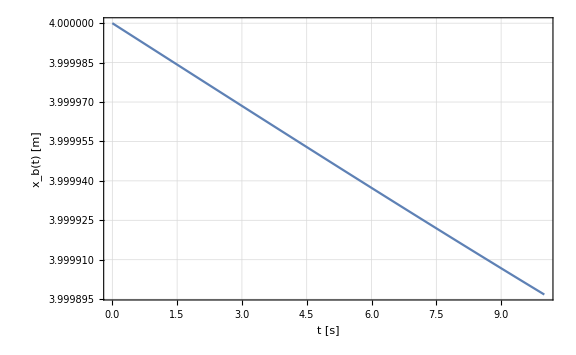
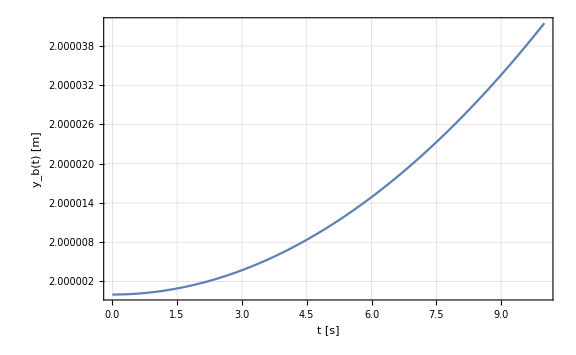
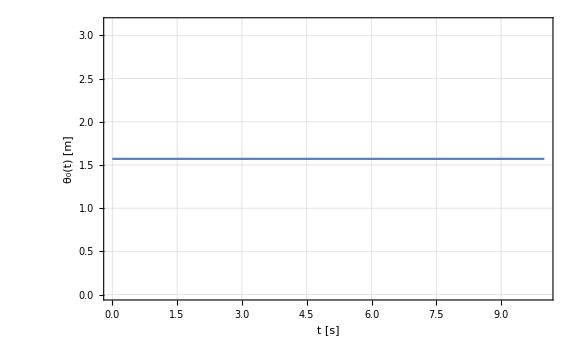
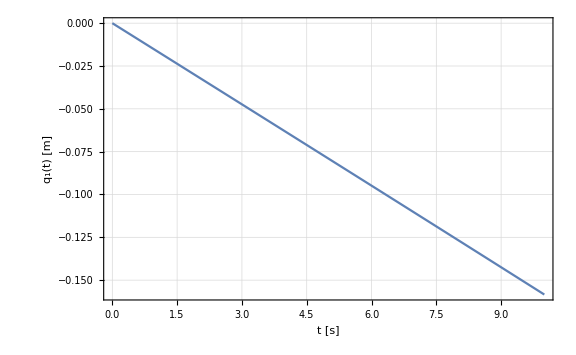
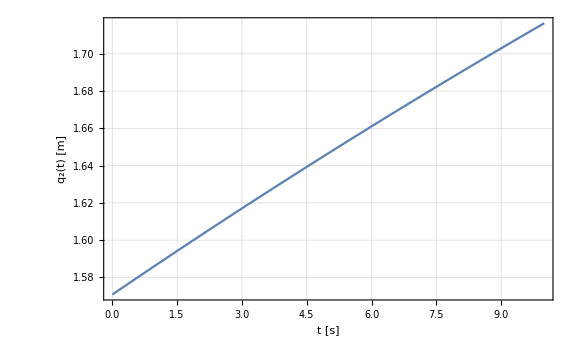

```mathematica
Row[{Plot[solMotion1[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

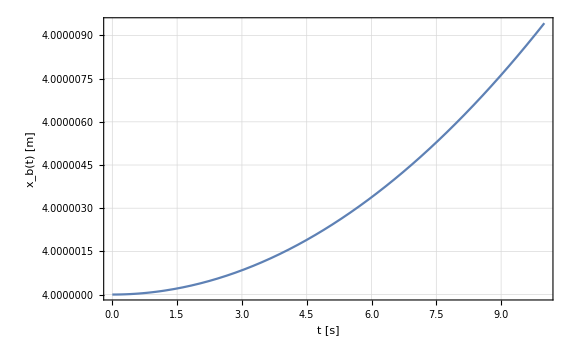
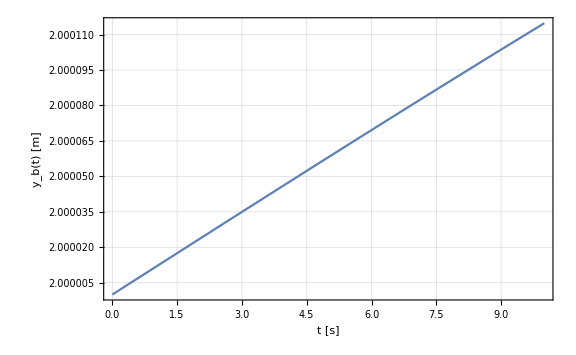
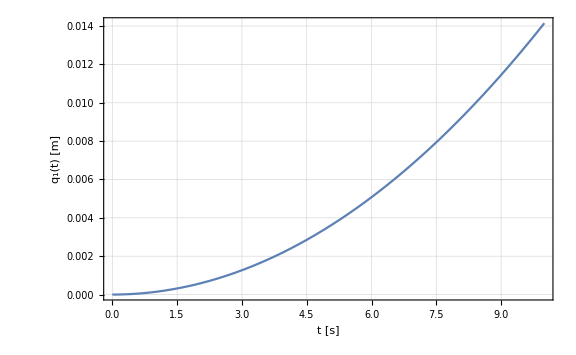
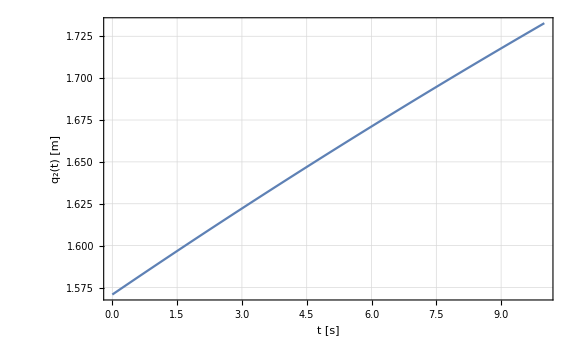
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotion2[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.paramScheme,O1[[1;;2]]/.param/.paramScheme,EE[[1;;2]]/.param/.paramScheme},PlotMarkers->{Automatic, 5}];
```

```mathematica
{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10}
{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10}
```

{{3.9999,2.00004},{4.88172,7.52005},{-0.707829,7.5913}}

{{4.00001,2.00011},{3.92091,7.58956},{-1.58257,6.60985}}

```mathematica
RobotPlotAfter1=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
RobotPlotAfter2=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
```

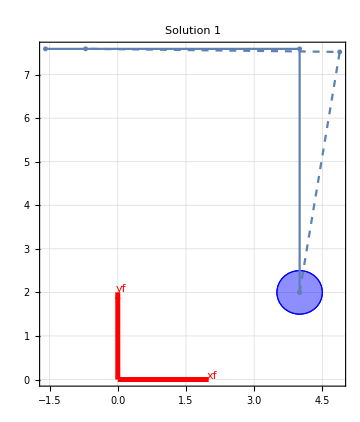
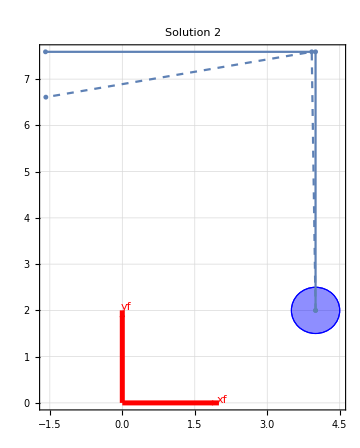

```mathematica
Row[{Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->10,r]}]],RobotPlot,RobotPlotAfter1,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 1",ImageSize->Medium],Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion2/.t->10,r]}]],RobotPlot,RobotPlotAfter2,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 2",ImageSize->Medium]}]
```

### Simulation with control

Let’s suppose a critical damped behaviour (i.e. ξ=1):

```mathematica
Kp=1IdentityMatrix[3];
Kv0=2 Sqrt[Kp];
Kv1=2 0.5 Sqrt[Kp];
Kv2=2 1.5 Sqrt[Kp];
```

```mathematica
pd={θ0[t],q1[t],q2[t]}/.paramScheme
pd'={0,0,0};
```

{π/2,0,π/2}

```mathematica
p3={θ0[t],q1[t],q2[t]};
p3'=D[p3,t];
```

```mathematica
U0=-Mp[[3;;5,3;;5]].(Kv0.(p3'-pd')+Kp.(p3-pd))+Cp[[3;;5]];
U1=-Mp[[3;;5,3;;5]].(Kv1.(p3'-pd')+Kp.(p3-pd))+Cp[[3;;5]];
U2=-Mp[[3;;5,3;;5]].(Kv2.(p3'-pd')+Kp.(p3-pd))+Cp[[3;;5]];
```

```mathematica
eqMotionControl10=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControl20=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControl30=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U0[[1]];
eqMotionControl40=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U0[[2]];
eqMotionControl50=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U0[[3]];
```

```mathematica
eqMotionControl11=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControl21=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControl31=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U1[[1]];
eqMotionControl41=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U1[[2]];
eqMotionControl51=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U1[[3]];
```

```mathematica
eqMotionControl12=Mp[[1,1;;5]].D[p,t,t]+Cp[[1]];
eqMotionControl22=Mp[[2,1;;5]].D[p,t,t]+Cp[[2]];
eqMotionControl32=Mp[[3,1;;5]].D[p,t,t]+Cp[[3]]-U2[[1]];
eqMotionControl42=Mp[[4,1;;5]].D[p,t,t]+Cp[[4]]-U2[[2]];
eqMotionControl52=Mp[[5,1;;5]].D[p,t,t]+Cp[[5]]-U2[[3]];
```

```mathematica
solMotionControl10=NDSolve[{(eqMotionControl10/.param)==0,(eqMotionControl20/.param)==0,(eqMotionControl30/.param)==0,(eqMotionControl40/.param)==0,(eqMotionControl51/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl20=NDSolve[{(eqMotionControl10/.param)==0,(eqMotionControl20/.param)==0,(eqMotionControl30/.param)==0,(eqMotionControl40/.param)==0,(eqMotionControl50/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

```mathematica
solMotionControl11=NDSolve[{(eqMotionControl11/.param)==0,(eqMotionControl21/.param)==0,(eqMotionControl31/.param)==0,(eqMotionControl41/.param)==0,(eqMotionControl51/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl21=NDSolve[{(eqMotionControl11/.param)==0,(eqMotionControl21/.param)==0,(eqMotionControl31/.param)==0,(eqMotionControl41/.param)==0,(eqMotionControl51/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

```mathematica
solMotionControl12=NDSolve[{(eqMotionControl12/.param)==0,(eqMotionControl22/.param)==0,(eqMotionControl32/.param)==0,(eqMotionControl42/.param)==0,(eqMotionControl52/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl22=NDSolve[{(eqMotionControl12/.param)==0,(eqMotionControl22/.param)==0,(eqMotionControl32/.param)==0,(eqMotionControl42/.param)==0,(eqMotionControl52/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

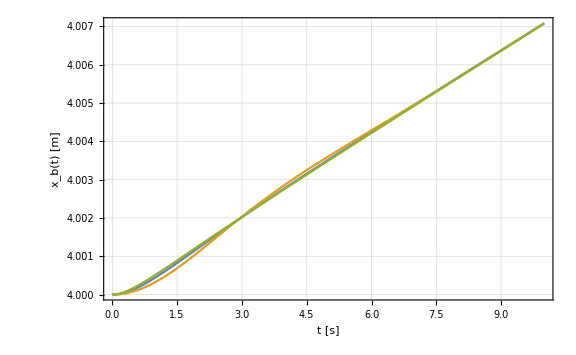
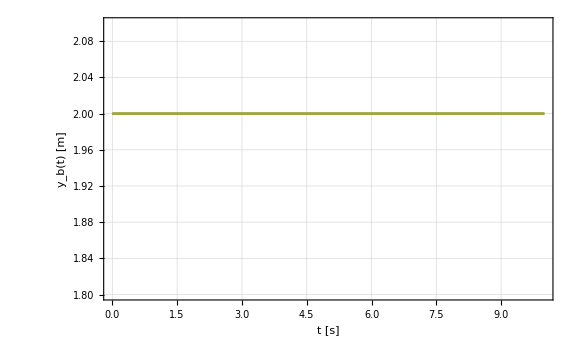
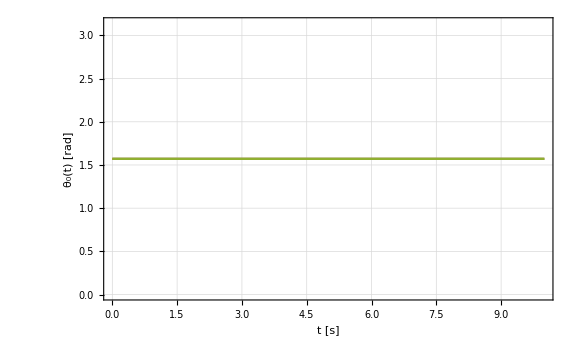
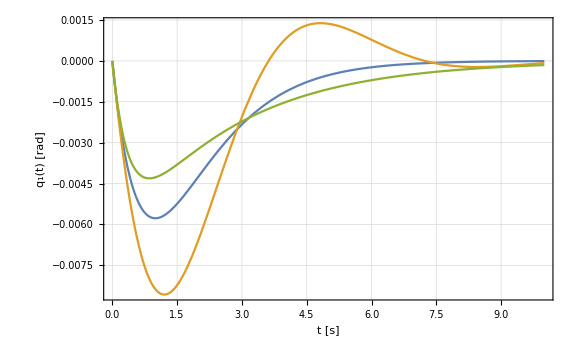
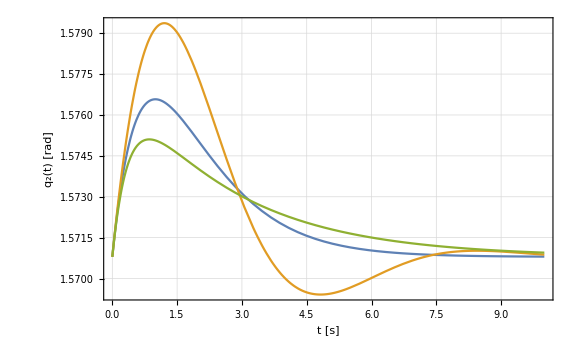

```mathematica
Row[{Plot[{solMotionControl10[[1,2]],solMotionControl11[[1,2]],solMotionControl12[[1,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[{solMotionControl10[[2,2]],solMotionControl11[[2,2]],solMotionControl12[[2,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.8,2.1}}],
Plot[{solMotionControl10[[3,2]],solMotionControl11[[3,2]],solMotionControl12[[3,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[{solMotionControl10[[4,2]],solMotionControl11[[4,2]],solMotionControl12[[4,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[{solMotionControl10[[5,2]],solMotionControl11[[5,2]],solMotionControl12[[5,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

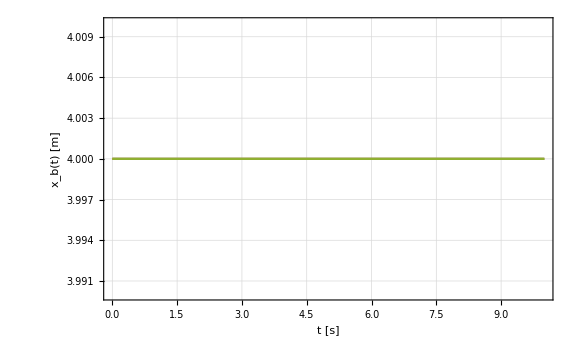
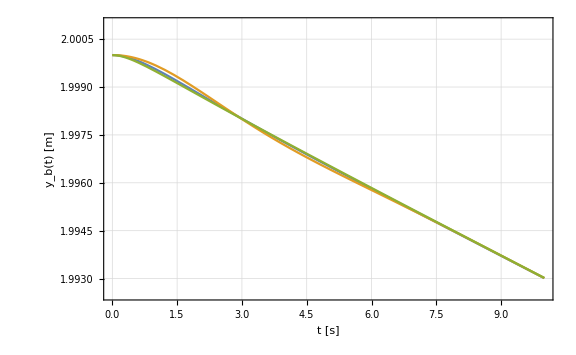
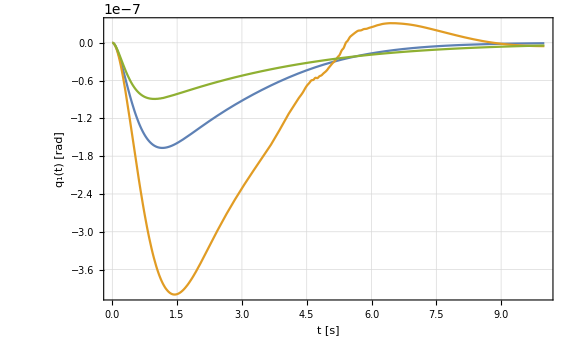
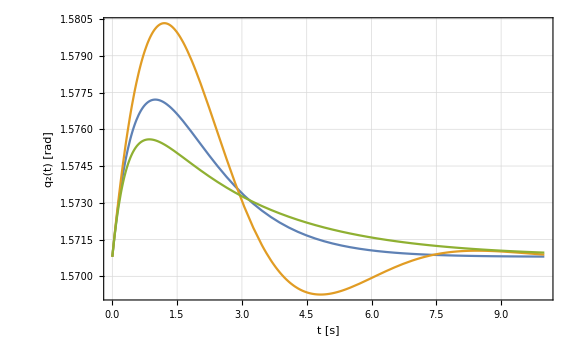
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[{solMotionControl20[[1,2]],solMotionControl21[[1,2]],solMotionControl22[[1,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{3.99,4.01}}],
Plot[{solMotionControl20[[2,2]],solMotionControl21[[2,2]],solMotionControl22[[2,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.9925,2.001}}],
Plot[{solMotionControl20[[3,2]],solMotionControl21[[3,2]],solMotionControl22[[3,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[{solMotionControl20[[4,2]],solMotionControl21[[4,2]],solMotionControl22[[4,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[{solMotionControl20[[5,2]],solMotionControl21[[5,2]],solMotionControl22[[5,2]]},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

### Simulation with uknown mass

```mathematica
Chop[Mp[[1;;5,1;;5]]/.paramScheme/.mb->Infinity/.mO->3000/.paramExtraction]//MatrixForm
```

(∞ | 0 | -19285.5 | -19285.5 | 0
0 | ∞ | -17137.4 | -17137.4 | -17137.4
-19285.5 | -17137.4 | ∞ | 200479. | 94235.9
-19285.5 | -17137.4 | 200479. | 200479. | 94235.9
0 | -17137.4 | 94235.9 | 94235.9 | 94235.9)

```mathematica
MpAss=Mp/.paramScheme;
CpAss=Cp/.paramScheme;
```

```mathematica
test=2000;
Mpstim=MpAss/.mO->test;
Cpstim=CpAss/.mO->test;
```

```mathematica
U=-(Mpstim/.paramScheme)[[3;;5,3;;5]].(Kv0.(p3'-pd')+Kp.(p3-pd))+(Cpstim[[3;;5]]/.paramScheme);
```

```mathematica
eqMotionControlStim1=MpAss[[1,1;;5]].D[p,t,t]+CpAss[[1]];
eqMotionControlStim2=MpAss[[2,1;;5]].D[p,t,t]+CpAss[[2]];
eqMotionControlStim3=MpAss[[3,1;;5]].D[p,t,t]+CpAss[[3]]-U[[1]];
eqMotionControlStim4=MpAss[[4,1;;5]].D[p,t,t]+CpAss[[4]]-U[[2]];
eqMotionControlStim5=MpAss[[5,1;;5]].D[p,t,t]+CpAss[[5]]-U[[3]];
```

```mathematica
solMotionControl1=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl2=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]];
```

```mathematica
solMotionControl1Data=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition1},{xb,yb,θ0,q1,q2},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]];
solMotionControl2Data=NDSolve[{(eqMotionControlStim1/.param)==0,(eqMotionControlStim2/.param)==0,(eqMotionControlStim3/.param)==0,(eqMotionControlStim4/.param)==0,(eqMotionControlStim5/.param)==0,NDinitialCondition2},{xb,yb,θ0,q1,q2},{t,0,10},Method->{"EquationSimplification"->"Residual"}][[1]];
```

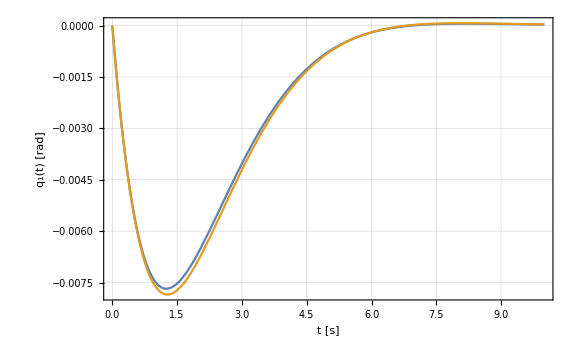

```mathematica
provaq11=Chop[Collect[Expand[Simplify@eqMotionControlStim4/.param/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,q2''[t]->0,θ0[t]->π/2,q2[t]->π/2,θ0'[t]->0,q2'[t]->0}],{q1[t],q1'[t],q1''[t]}]];
finalq11=Chop[provaq11/MpAss[[4,4]]/.param//Simplify];
graficoq11=NDSolve[{provaq11==0,q1[0]==0,q1'[0]==pf1'[[4]]},q1[t],{t,0,10}][[1]];
Plot[{solMotionControl1[[4,2]],q1[t]/.graficoq11},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

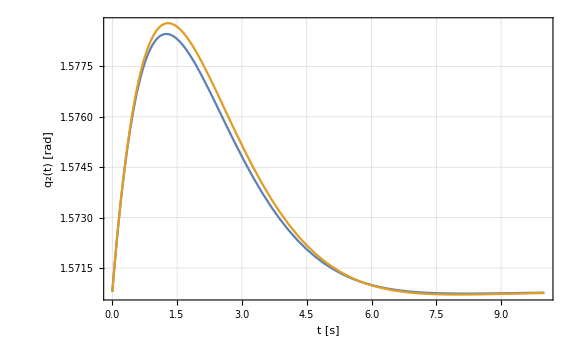

```mathematica
provaq21=Chop[Collect[Expand[Simplify@eqMotionControlStim5/.param/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,q1''[t]->0,θ0[t]->π/2,q1[t]->0,θ0'[t]->0,q1'[t]->0}],{q2[t],q2'[t],q2''[t]}]];
finalq21=Chop[provaq21/MpAss[[5,5]]/.param//Simplify];
graficoq21=NDSolve[{provaq21==0,q2[0]==π/2,q2'[0]==pf1'[[5]]},q2[t],{t,0,10}][[1]];
Plot[{solMotionControl1[[5,2]],q2[t]/.graficoq21},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

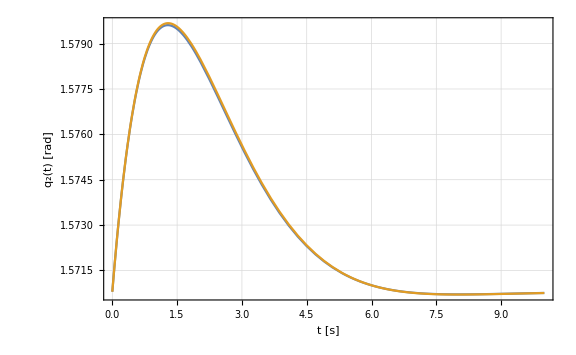

```mathematica
provaq22=Chop[Collect[Expand[Simplify@eqMotionControlStim5/.param/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,q1''[t]->0,θ0[t]->π/2,q1[t]->0,θ0'[t]->0,q1'[t]->0}],{q2[t],q2'[t],q2''[t]}]];
finalq22=Chop[provaq22/MpAss[[5,5]]/.param//Simplify];
graficoq22=NDSolve[{provaq22==0,q2[0]==π/2,q2'[0]==pf2'[[5]]},q2[t],{t,0,10}][[1]];
Plot[{solMotionControl2[[5,2]],q2[t]/.graficoq22},{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]
```

#### Nonlinearfit Symbolic Form

```mathematica
q11Data=Transpose@{solMotionControl1Data[[4,2,3]][[1]],solMotionControl1Data[[4,2,4,3,1;;348;;3]]};
q21Data=Transpose@{solMotionControl1Data[[5,2,3]][[1]],solMotionControl1Data[[5,2,4,3,1;;348;;3]]};
q12Data=Transpose@{solMotionControl2Data[[4,2,3]][[1]],solMotionControl2Data[[4,2,4,3,1;;297;;3]]};
q22Data=Transpose@{solMotionControl2Data[[5,2,3]][[1]],solMotionControl2Data[[5,2,4,3,1;;297;;3]]};
```

```mathematica
eqApprox1=Chop[Collect[Expand[Simplify@eqMotionControlStim4/.paramExtraction/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,q2''[t]->0,θ0[t]->π/2,q2[t]->π/2,θ0'[t]->0,q2'[t]->0}],{q1[t],q1'[t],q1''[t]}]]
eqApprox2=Chop[Collect[Expand[Simplify@eqMotionControlStim5/.paramExtraction/.{xb''[t]->0,yb''[t]->0,xb'[t]->0,yb'[t]->0,θ0''[t]->0,q1''[t]->0,θ0[t]->π/2,q1[t]->0,θ0'[t]->0,q1'[t]->0}],{q2[t],q2'[t],q2''[t]}]]
```

138861. q1[t]+277722. q1'[t]+(15624.+61.6185 mO) q1''[t]

-100320.+63865.6 q2[t]+127731. q2'[t]+(3124.81+30.3704 mO) q2''[t]

```mathematica
sol11=DSolve[{eqApprox1==0,q1[0]==q10,q1'[0]==pf1'[[4]]},q1[t],t][[1]];
sol21=DSolve[{eqApprox2==0,q2[0]==q20,q2'[0]==pf1'[[5]]},q2[t],t][[1]];
sol12=DSolve[{eqApprox1==0,q1[0]==q10,q1'[0]==pf2'[[4]]},q1[t],t][[1]]
sol22=DSolve[{eqApprox2==0,q2[0]==q20,q2'[0]==pf2'[[5]]},q2[t],t][[1]];
```

{q1[t]→0}

```mathematica
table1=Table[Plot[q1[t]/.sol11/.mO->300*i,{t,0,10},PlotRange->{Automatic,{0.001,-0.011}},PlotStyle->ColorData[i+77,"ColorFunction"],PlotLegends->Placed[LineLegend[{Row[{"m = ",300*i," kg"}]}],{1,0.5}],Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [rad]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],{i,1,15}];
Show[table1]
```

-Graphics-

```mathematica
nlmq11Symb=NonlinearModelFit[q11Data,q1[t]/.sol11,{{mO,1999}},t]
nlmq11Symb["ParameternlTable"]
real11Symbolic=nlmq11Symb["ParameterTableEntries"][[1,1]]
```

FittedModel[(0.-5.52588×10^-6 ⅈ) (3158.95 ⅇ^((-0.71339-0.452178 ⅈ) t)-3158.95 ⅇ^((-0.71339+0.452178 ⅈ) t))]

FittedModel[(0.-5.52588×10^-6 ⅈ) (3158.95 ⅇ^((-0.71339-0.452178 ⅈ) t)-3158.95 ⅇ^((-0.71339+0.452178 ⅈ) t))][ParameternlTable]

2905.39

```mathematica
nlmq11Symb["ParameterTable"][[1]]
```

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2905.39 | 0.67178 | 4324.9 | 1.6724×10^-301

```mathematica
nlmq21Symb=NonlinearModelFit[q21Data,q2[t]/.sol21,{{mO,1999}},t]
nlmq21Symb["ParameterTable"]
real21Symbolic=nlmq21Symb["ParameterTableEntries"][[1,1]]
```

FittedModel[(0.-0.0344944 ⅈ) ((0.+45.5378 ⅈ)-(0.506572-3.21856×10^-15 ⅈ) ⅇ^((«1») t)+(0.506572+3.21856×10^-15 ⅈ) ⅇ^((-0.714461+0.451671 ⅈ) t))]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2840.43 | 0.640823 | 4432.48 | 9.91428×10^-303

2840.43

```mathematica
nlmq22Symb=NonlinearModelFit[q22Data,q2[t]/.sol22,{{mO,0}},t]
nlmq22Symb["ParameterTable"]
real22Symbolic=nlmq22Symb["ParameterTableEntries"][[1,1]]
```

FittedModel[(0.-0.0320627 ⅈ) ((0.+48.9914 ⅈ)-(0.588327-3.46266×10^-15 ⅈ) ⅇ^((«1») t)+(0.588327+3.46266×10^-15 ⅈ) ⅇ^((-0.683725+0.465022 ⅈ) t))]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2972.75 | 0.13173 | 22567. | 0.

2972.75

#### Nonlinear Model Fit

```mathematica
nlmq11=NonlinearModelFit[q11Data,{(pf1'[[4]]/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t]},{{ω,0.7},{xi,0.7}},t];
```

```mathematica
nlmq11["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.843663 | 3.14532×10^-7 | 2.68228×10^6 | 0.
xi | 0.843661 | 7.91565×10^-7 | 1.06581×10^6 | 0.

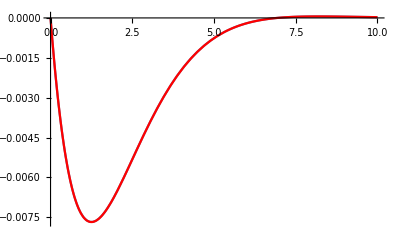

```mathematica
Show[ListLinePlot[q11Data],Plot[nlmq11[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
real11=(Mpstim[[4,4]]/.param/.paramScheme)/(nlmq11["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal11=Solve[Mp[[4,4]]-real11==0,mO][[1,1,2]]/.param/.paramScheme
```

2912.6

```mathematica
q21Data=Transpose@{solMotionControl1Data[[5,2,3]][[1]],solMotionControl1Data[[5,2,4,3,1;;348;;3]]};
```

```mathematica
nlmq21=NonlinearModelFit[q21Data,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf1'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[1/2 π (1-1.86519 ⅇ^(-0.712723 t) Sin[0.565857+0.452678 t])+ⅇ^(-0.712723 t) (1/2 π Cos[0.452678 t]+2.50803 Sin[0.452678 t])]

```mathematica
nlmq21["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.844328 | 0.0000186541 | 45262.2 | 0.
xi | 0.84413 | 0.0000469253 | 17988.8 | 0.

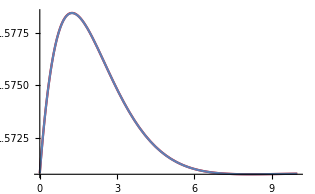

```mathematica
Show[Plot[nlmq21[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q21Data]]
```

```mathematica
real21=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq21["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal21=Solve[Mp[[5,5]]-real21==0,mO][[1,1,2]]/.param/.paramScheme
```

2848.31

```mathematica
q22Data=Transpose@{solMotionControl2Data[[5,2,3]][[1]],solMotionControl2Data[[5,2,4,3,1;;297;;3]]};
```

```mathematica
nlmq22=NonlinearModelFit[q22Data,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf2'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[1/2 π (1-1.77796 ⅇ^(-0.683697 t) Sin[0.597337+0.465074 t])+ⅇ^(-0.683697 t) (1/2 π Cos[0.465074 t]+2.34692 Sin[0.465074 t])]

```mathematica
nlmq22["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.826883 | 0.0000242682 | 34072.7 | 0.
xi | 0.826836 | 0.0000602262 | 13728.9 | 8.22877×10^-307

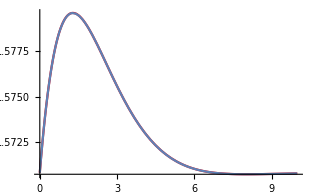

```mathematica
Show[Plot[nlmq22[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q22Data]]
```

```mathematica
real22=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq22["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal22=Solve[Mp[[5,5]]-real22==0,mO][[1,1,2]]/.param/.paramScheme
```

2973.05

```mathematica
Mean[{mreal11,mreal21}]
Mean[{mreal12,mreal22}]
```

2880.46

1/2 (2973.05+mreal12)

#### Nonlinearfit Symbolic Form with noise

```mathematica
w=WhiteNoiseProcess[0.001];
noiseData1=RandomFunction[w,{0,115}];
noiseData1y=Normal[noiseData1][[1,All,2]];
noiseData2=RandomFunction[w,{0,98}];
noiseData2y=Normal[noiseData2][[1,All,2]];
```

```mathematica
q11DataNoise=Transpose@{q11Data[[All,1]],q11Data[[All,2]]+noiseData1y};
q21DataNoise=Transpose@{q21Data[[All,1]],q21Data[[All,2]]+noiseData1y};
q12DataNoise=Transpose@{q12Data[[All,1]],q12Data[[All,2]]+noiseData2y};
q22DataNoise=Transpose@{q22Data[[All,1]],q22Data[[All,2]]+noiseData2y};
```

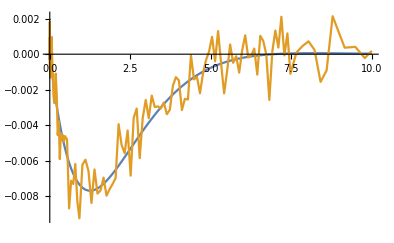

```mathematica
ListLinePlot[{q11Data,q11DataNoise}]
```

```mathematica
nlmq11Symb=NonlinearModelFit[q11DataNoise,q1[t]/.sol11,{{mO,1999}},t]
nlmq11Symb["ParameterTable"]
real11Symbolic=nlmq11Symb["ParameterTableEntries"][[1,1]]
```

FittedModel[(0.-5.81453×10^-6 ⅈ) (3071.29 ⅇ^((-0.733751-0.441996 ⅈ) t)-3071.29 ⅇ^((-0.733751+0.441996 ⅈ) t))]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2817.73 | 81.1328 | 34.7298 | 8.41904×10^-63

2817.73

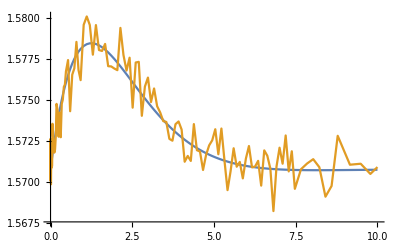

```mathematica
ListLinePlot[{q21Data,q21DataNoise}]
```

```mathematica
nlmq21Symb=NonlinearModelFit[q21DataNoise,q2[t]/.sol21,{{mO,1999}},t]
nlmq21Symb["ParameterTable"]
real21Symbolic=nlmq21Symb["ParameterTableEntries"][[1,1]]
```

FittedModel[(0.-0.0330981 ⅈ) ((0.+47.4588 ⅈ)-(0.519033-3.35434×10^-15 ⅈ) ⅇ^((«1») t)+(0.519033+3.35434×10^-15 ⅈ) ⅇ^((-0.697308+0.459423 ⅈ) t))]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 2912.84 | 75.5839 | 38.5378 | 1.3717×10^-67

2912.84

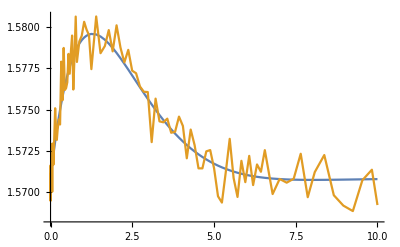

```mathematica
ListLinePlot[{q22Data,q22DataNoise}]
```

```mathematica
nlmq22Symb=NonlinearModelFit[q22DataNoise,q2[t]/.sol22,{{mO,0}},t]
nlmq22Symb["ParameterTable"]
real22Symbolic=nlmq22Symb["ParameterTableEntries"][[1,1]]
```

FittedModel[(0.-0.0316098 ⅈ) ((0.+49.6933 ⅈ)-(0.593697-3.51227×10^-15 ⅈ) ⅇ^((«1») t)+(0.593697+3.51227×10^-15 ⅈ) ⅇ^((-0.677541+0.467418 ⅈ) t))]

| Estimate | Standard Error | t-Statistic | P-Value
mO | 3000.82 | 77.2736 | 38.8337 | 2.54944×10^-61

3000.82

```mathematica
Mean[{real11Symbolic,real21Symbolic}]
```

2865.28

#### Nonlinear Model Fit with noise

```mathematica
nlmq11=NonlinearModelFit[q11DataNoise,{(pf1'[[4]]/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t]},{{ω,0.7},{xi,0.7}},t];
```

```mathematica
nlmq11["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.865183 | 0.0150675 | 57.4206 | 5.59987×10^-86
xi | 0.825879 | 0.0362613 | 22.7758 | 3.08153×10^-44

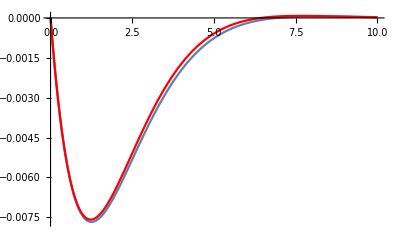

```mathematica
Show[ListLinePlot[q11Data],Plot[nlmq11[t],{t,0,10},PlotStyle->Red]]
```

```mathematica
real11=(Mpstim[[4,4]]/.param/.paramScheme)/(nlmq11["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal11=Solve[Mp[[4,4]]-real11==0,mO][[1,1,2]]/.param/.paramScheme
```

3050.41

```mathematica
nlmq21=NonlinearModelFit[q21DataNoise,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf1'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[1/2 π (1-1.97091 ⅇ^(-0.709648 t) Sin[0.53214+0.417838 t])+ⅇ^(-0.709648 t) (1/2 π Cos[0.417838 t]+2.70559 Sin[0.417838 t])]

```mathematica
nlmq21["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.823522 | 0.013783 | 59.7491 | 6.96477×10^-88
xi | 0.861723 | 0.0362526 | 23.7699 | 5.47426×10^-46

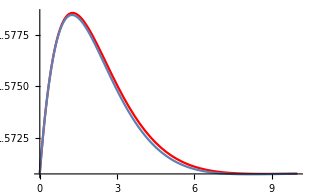

```mathematica
Show[Plot[nlmq21[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q21Data]]
```

```mathematica
real21=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq21["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal21=Solve[Mp[[5,5]]-real21==0,mO][[1,1,2]]/.param/.paramScheme
```

2729.03

```mathematica
nlmq22=NonlinearModelFit[q22DataNoise,{q20(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(pf2'[[5]]+q20 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t]},{{ω,0.7},{xi,0.7}},t]
```

FittedModel[1/2 π (1-1.69009 ⅇ^(-0.661483 t) Sin[0.633146+0.485492 t])+ⅇ^(-0.661483 t) (1/2 π Cos[0.485492 t]+2.17635 Sin[0.485492 t])]

```mathematica
nlmq22["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
ω | 0.820525 | 0.0136817 | 59.9725 | 1.77671×10^-78
xi | 0.80617 | 0.033663 | 23.9483 | 1.65233×10^-42

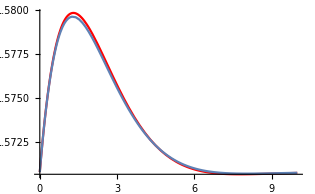

```mathematica
Show[Plot[nlmq22[t],{t,0,10},PlotStyle->Red,PlotRange->All],ListLinePlot[q22Data]]
```

```mathematica
real22=(Mpstim[[5,5]]/.param/.paramScheme)/(nlmq22["ParameterTableEntries"][[2,1]])^2;
```

```mathematica
mreal22=Solve[Mp[[5,5]]-real22==0,mO][[1,1,2]]/.param/.paramScheme
```

3132.77

#### Parametric Plot Symbolic

Per la simulazion 12, l’approssimazione è troppo simile al valore vero, per cui questo metodo non converge.

```mathematica
{disp11,time11}=FindMinimum[solMotionControl1[[4,2]],{t,1,4}];
{disp21,time21}=FindMaximum[solMotionControl1[[5,2]],{t,1,2}];
{disp12,time12}=FindMaximum[solMotionControl2[[4,2]],{t,1,4}];
{disp22,time22}=FindMaximum[solMotionControl2[[5,2]],{t,1,4}];
```

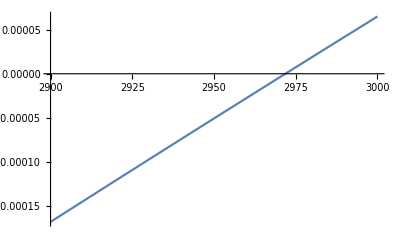

```mathematica
Plot[FullSimplify@(sol22[[1,2]]/.t->time22[[1,2]])-disp22,{mO,2900,3000}]
```

```mathematica
mreal11=FindRoot[FullSimplify@(sol11[[1,2]]/.t->time11[[1,2]])-disp11,{mO,1000,10000}][[1,2]]
mreal21=FindRoot[FullSimplify@(sol21[[1,2]]/.t->time21[[1,2]])-disp21,{mO,2000,4000}][[1,2]]
mreal22=FindRoot[FullSimplify@(sol22[[1,2]]/.t->time22[[1,2]])-disp22,{mO,2900,3000}][[1,2]]
```

2914.77

2862.73

2972.11

```mathematica
Mean[{mreal11,mreal21}]
Mean[{mreal22}]
```

2888.75

2972.11

```mathematica
(1-Mean[{mreal11,mreal21}]/mO/.param)*100
(1-Mean[{mreal22}]/mO/.param)*100
```

3.70837

0.929612

#### Parametric Plot

```mathematica
D[(q0'/(ω Sqrt[1-xi^2])) Exp[-xi ω t]Sin[Sqrt[1-xi^2]ω t],t]//Simplify
FullSimplify[D[q0(1-(Exp[-xi ω t])/( Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t+ArcCos[xi]])+(q20 Cos[ω Sqrt[1-xi^2] t]+(q0'+q0 xi ω)/(ω Sqrt[1-xi^2])Sin[Sqrt[1-xi^2]ω t])Exp[-xi ω t],t]]/.q0->q20
```

ⅇ^(-t xi ω) (Cos[t √(1-xi^2) ω]-(xi Sin[t √(1-xi^2) ω])/(√(1-xi^2))) q0'

(ⅇ^(-t xi ω) (√(1-xi^2) Cos[t √(1-xi^2) ω]-xi Sin[t √(1-xi^2) ω]) (π/2)')/(√(1-xi^2))

```mathematica
ωd=Simplify[Sqrt[1-mtest/m]Sqrt[mtest/m]];
β=Simplify[Sqrt[1-mtest/m]/Sqrt[mtest/m]];
```

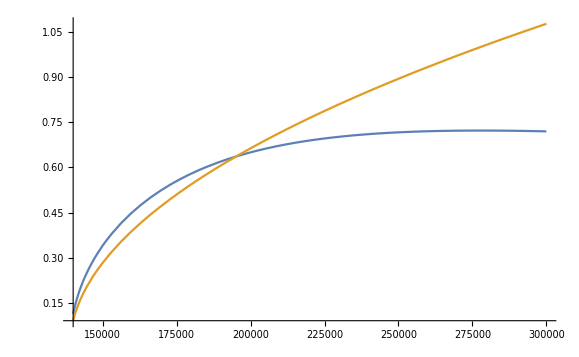

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time11[[1,2]]],β/.mtest->Mpstim[[4,4]]/.param/.paramScheme},{m,140000,300000}]
```

```mathematica
real11=FindRoot[Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time11[[1,2]]]-β/.mtest->Mpstim[[4,4]]/.param/.paramScheme,{m,150000,200000}]
mreal11=Solve[Mp[[4,4]]-real11[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→195090.}

2912.54

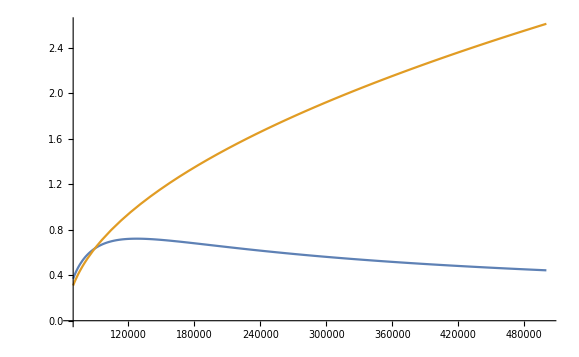

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time21[[1,2]]],β/.mtest->Mpstim[[5,5]]/.param/.paramScheme},{m,70000,500000}]
```

```mathematica
real21=FindRoot[Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time21[[1,2]]]-β/.mtest->Mpstim[[5,5]]/.param/.paramScheme,{m,80000,100000}]
mreal21=Solve[Mp[[5,5]]-real21[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→89665.5}

2849.51

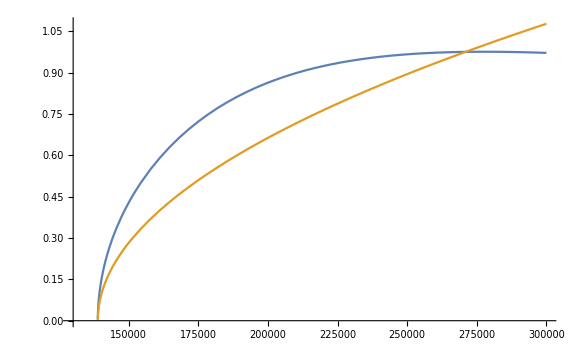

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time12[[1,2]]],β/.mtest->Mpstim[[4,4]]/.param/.paramScheme},{m,130000,300000}]
```

```mathematica
real12=FindRoot[Tan[(ωd/.mtest->Mpstim[[4,4]]/.param/.paramScheme) time21[[1,2]]]-β/.mtest->Mpstim[[4,4]]/.param/.paramScheme,{m,187000,200000}]
mreal12=Solve[Mp[[4,4]]-real12[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→194957.}

2910.38

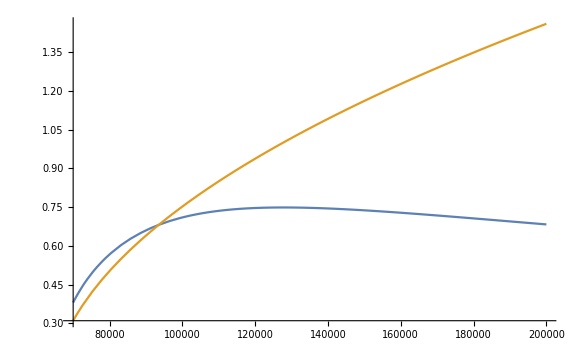

```mathematica
Plot[{Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time22[[1,2]]],β/.mtest->Mpstim[[5,5]]/.param/.paramScheme},{m,70000,200000}]
```

```mathematica
real22=FindRoot[Tan[(ωd/.mtest->Mpstim[[5,5]]/.param/.paramScheme) time22[[1,2]]]-β/.mtest->Mpstim[[5,5]]/.param/.paramScheme,{m,70000,100000}]
mreal22=Solve[Mp[[5,5]]-real22[[1,2]]==0,mO][[1,1,2]]/.param/.paramScheme
```

{m→93492.8}

2975.53

```mathematica
Mean[{mreal11,mreal21}]
Mean[{mreal12,mreal22}]
```

2881.02

2942.95

```mathematica
(1-Mean[{mreal11,mreal21}]/mO/.param)*100
(1-Mean[{mreal12,mreal22}]/mO/.param)*100
```

3.96588

1.90152

## Kinetic Parameters Extraction

```mathematica
initialConditionsSymbolic={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0};
```

Initial object’s velocities without knowing Ω’[t]:

```mathematica
solVel1=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme)[[1]]]==ψf1'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme)[[2]]]==ψf1'[[2]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme)[[3]]]==ψf1'[[3]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
solVel2=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme)[[1]]]==ψf2'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme)[[2]]]==ψf2'[[2]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme)[[3]]]==ψf2'[[3]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
```

realmass1 (-1.06599×10^141-1.30261×10^139 realmass1-2.59031×10^136 realmass1^2+1.73836×10^118 realmass1^3+1.00943×10^116 realmass1^4+1.60136×10^98 realmass1^5-2.50505×10^93 realmass1^6+9.76568×10^73 realmass1^7+1.65316×10^70 realmass1^8)≠0&&xO'[t]==(2.10175×10^-8 (-1.79006×10^150-2.63493×10^148 realmass1-9.81837×10^145 realmass1^2-1.08746×10^143 realmass1^3+1.08347×10^126 realmass1^4+6.16153×10^122 realmass1^5-4.68601×10^105 realmass1^6-1.37483×10^100 realmass1^7+4.99945×10^82 realmass1^8+7.5917×10^76 realmass1^9))/(realmass1 (-1.06599×10^141-1.30261×10^139 realmass1-2.59031×10^136 realmass1^2+1.73836×10^118 realmass1^3+1.00943×10^116 realmass1^4+1.60136×10^98 realmass1^5-2.50505×10^93 realmass1^6+9.76568×10^73 realmass1^7+1.65316×10^70 realmass1^8))&&yO'[t]==0&&Ω'[t]==0&&-1.23218×10^33-1.50569×10^31 realmass1-2.99415×10^28 realmass1^2+1.59943×10^11 realmass1^3+371873. realmass1^4≠0

realmass2 (-1.06599×10^141-1.30261×10^139 realmass2-2.59031×10^136 realmass2^2+1.73836×10^118 realmass2^3+1.00943×10^116 realmass2^4+1.60136×10^98 realmass2^5-2.50505×10^93 realmass2^6+9.76568×10^73 realmass2^7+1.65316×10^70 realmass2^8)≠0&&xO'[t]==(1.96226×10^21 (5.031×10^104+1.43124×10^103 realmass2-9.52672×10^99 realmass2^2-2.0168×10^99 realmass2^3-4.77591×10^96 realmass2^4+6.59489×10^90 realmass2^5+2.23923×10^76 realmass2^6-2.50619×10^70 realmass2^7-1.44488×10^53 realmass2^8+3.10252×10^47 realmass2^9))/(realmass2 (-1.06599×10^141-1.30261×10^139 realmass2-2.59031×10^136 realmass2^2+1.73836×10^118 realmass2^3+1.00943×10^116 realmass2^4+1.60136×10^98 realmass2^5-2.50505×10^93 realmass2^6+9.76568×10^73 realmass2^7+1.65316×10^70 realmass2^8))&&yO'[t]==0&&Ω'[t]==0&&-1.23218×10^33-1.50569×10^31 realmass2-2.99415×10^28 realmass2^2+1.59943×10^11 realmass2^3+371873. realmass2^4≠0

Initial object' s velocities knowing Ω'[t] :

```mathematica
solVel1Acc=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme/.Ω'[t]->0)[[1]]]==ψf1'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass1/.param/.paramScheme/.Ω'[t]->0)[[2]]]==ψf1'[[2]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
solVel2Acc=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme/.Ω'[t]->0)[[1]]]==ψf2'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.mO->realmass2/.param/.paramScheme/.Ω'[t]->0)[[2]]]==ψf2'[[2]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
```

xO'[t]==0.100141&&yO'[t]==8.64344×10^-6

xO'[t]==0&&yO'[t]==-0.0999938

```mathematica
momentumEq1=Chop@Simplify[M.(p'/.{p'[[1]]->pf1'[[1]],p'[[2]]->pf1'[[2]],p'[[3]]->pf1'[[3]],p'[[4]]->pf1'[[4]],p'[[5]]->pf1'[[5]]})+Transpose[J].Transpose[pseudoInverseJop].Mo.(({xO'[t],yO'[t],Ω'[t]}/.{xO'[t]->ψf1'[[1]],yO'[t]->ψf1'[[2]],Ω'[t]->ψf1'[[3]]})-({xO'[t],yO'[t],Ω'[t]}))/.paramExtraction/.mO->realmass1/.paramScheme/.Ω'[t]->0]
Solve[{momentumEq1[[1]]==0,momentumEq1[[2]]==0},{xO'[t],yO'[t]}][[1]]
```

{296.856-2964.37 xO'[t],0.0252586-2922.28 yO'[t],-1659.56+16570.8 xO'[t]+16335.6 yO'[t],-1659.56+16570.8 xO'[t]+16335.6 yO'[t],-0.141196+16335.6 yO'[t]}

{xO'[t]→0.100141,yO'[t]→8.64344×10^-6}

```mathematica
momentumEq2=Chop@Simplify[M.(p'/.{p'[[1]]->pf2'[[1]],p'[[2]]->pf2'[[2]],p'[[3]]->pf2'[[3]],p'[[4]]->pf2'[[4]],p'[[5]]->pf2'[[5]]})+Transpose[J].Transpose[pseudoInverseJop].Mo.(({xO'[t],yO'[t],Ω'[t]}/.{xO'[t]->ψf2'[[1]],yO'[t]->ψf2'[[2]],Ω'[t]->ψf2'[[3]]})-({xO'[t],yO'[t],Ω'[t]}))/.paramExtraction/.mO->realmass2/.paramScheme/.Ω'[t]->0]
sol2=Solve[{momentumEq2[[1]]==0,momentumEq2[[2]]==0},{xO'[t],yO'[t]}][[1]]
```

{-2997.77 xO'[t],-295.503-2955.21 yO'[t],1651.86+16757.5 xO'[t]+16519.6 yO'[t],1651.86+16757.5 xO'[t]+16519.6 yO'[t],1651.86+16519.6 yO'[t]}

{xO'[t]→0.,yO'[t]→-0.0999938}